```mathematica
PartitionType[sets_]:=Sort[Map[Length[#]&,sets],#1>#2&]
```

```mathematica
PartitionType2[s_]:=PartitionType[SymbolToSets[s]]
```

```mathematica
PartitionTypeLabel[p_]:=StringJoin[ Map[ToString[#]&,p]]
```

```mathematica
DeleteDuplicates[ListofVars[allGraphs5[K5Key,"colofourrealnull"]]/.repFiveT]
```

{{2,2,1},{1,1,1,1,1},{5},{4,1},{3,2},{3,1,1},{2,1,1,1}}

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[prefix<>StringDrop[SymbolName[s],1]]
```

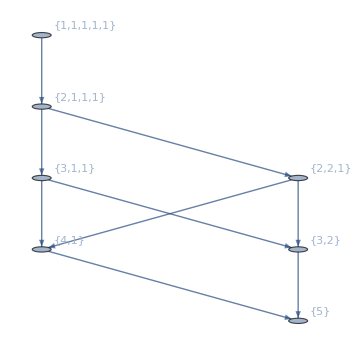

311

```mathematica
Graph[DeleteDuplicates[EdgeList[FormulaGraph[allGraphs5[0,"colofour"]]]/.repFiveT],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->{100,100}]
```

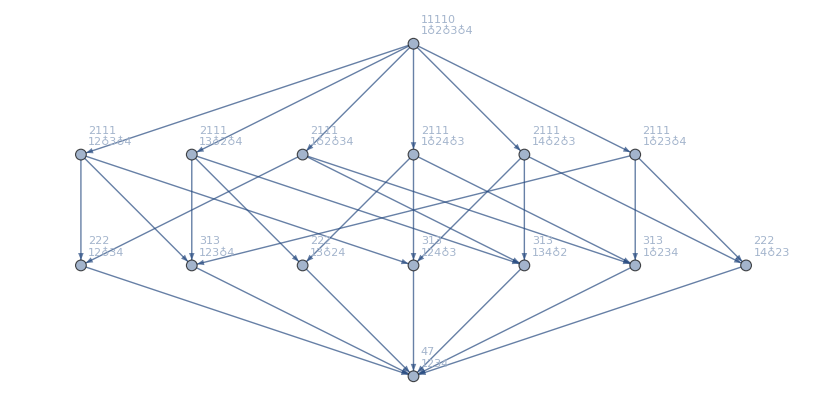

```mathematica
With[
{g=MobiusGraph4[K4Key,allGraphs4]},
Graph[EdgeList[g],VertexLabels->Table[k->Column[{
Framed[Row[{Style[PartitionTypeLabel[PartitionType2[k]],Red],Style[VertexInDegree[g,k],Bold]}],Background->White],
SymbolToLabel[k]
}],{k,VertexList[g]}],
GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
StirlingS2[2,2]
```

1

## Six does the same

```mathematica
repSixT=Table[allGraphs6[k,"colofourrealnull"]->PartitionType2[allGraphs6[k,"colofourrealnull"]],{k,allGraphs6NullAtomKeys}];
```

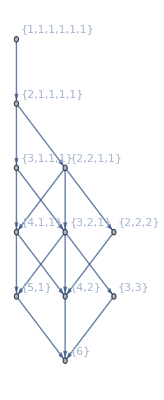

```mathematica
Graph[EdgeList[MobiusGraph5[K6Key,allGraphs6]]/.repSixT//DeleteDuplicates,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

## Lets do it for 5

## Lets do it for 6

```mathematica
MatrixForm[matFull,TableHeadings->{Map[SymbolToLabel[#]&,Table[allGraphs6[m,"colofourrealnull"],{m,allGraphs6NullAtomKeys}]],Map[Rotate[ SymbolToLabel[#],Pi/2]&,parts]}]
```

( | 1♁1♁1♁1♁1♁1 | 2♁1♁1♁1♁1 | 2♁2♁1♁1 | 2♁2♁2 | 3♁1♁1♁1 | 3♁2♁1 | 3♁3 | 4♁1♁1 | 4♁2 | 5♁1 | 6
1♁2♁3♁4♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
12♁3♁4♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
123♁4♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1234♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 1
12345♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
123456 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1
12346♁5 | 0 | 0 | 0 | 0 | 1 | 3 | 1 | 3 | 3 | 3 | 1
1234♁56 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 0 | 1
1235♁4♁6 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 1 | 3 | 2 | 1
12356♁4 | 0 | 1 | 6 | 3 | 4 | 16 | 4 | 6 | 7 | 4 | 1
1235♁46 | 1 | 15 | 45 | 15 | 20 | 60 | 10 | 15 | 15 | 6 | 1)

```mathematica
mat15=Table[Part5Coeff2[allGraphs5[k,"colofourrealnull"]/.RepNul5],{k,allGraphs5AtomKeys}]//DeleteDuplicates//Sort
```

{{0,0,0,0,0,0,1},{0,0,0,0,0,1,-1},{0,0,0,0,1,0,-1},{0,0,0,1,-1,-2,2},{0,0,1,0,-2,-1,2},{0,1,-3,-3,5,6,-6},{1,-10,15,20,-20,-30,24}}

```mathematica
MatrixForm[mat15,
 TableHeadings->{Map[SymbolToLabel[#]&,Table[allGraphs5[m,"colofour"],{m,allGraphs5AtomKeys}]],Map[Rotate[ SymbolToLabel[#],Pi/2]&,parts5]}, TableSpacing->{2,2}]
```

( | 1♁1♁1♁1♁1 | 2♁1♁1♁1 | 2♁2♁1 | 3♁1♁1 | 3♁2 | 4♁1 | 5
1♁2♁3♁4♁5 | 1 | -10 | 15 | 20 | -20 | -30 | 24
1♁2♁3♁45 | 0 | 1 | -3 | -3 | 5 | 6 | -6
1♁2♁35♁4 | 0 | 0 | 1 | 0 | -2 | -1 | 2
1♁2♁34♁5 | 0 | 0 | 0 | 1 | -1 | -2 | 2
1♁2♁345 | 0 | 0 | 0 | 0 | 1 | 0 | -1
1♁25♁3♁4 | 0 | 0 | 0 | 0 | 0 | 1 | -1
1♁25♁34 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Total[{1,-10, 15, 20,-20,-30 ,24}]
```

0

```mathematica
parts2=Sort[Table[PartitionTypeToSymbol[PartitionType2[allGraphs6[k,"colofourrealnull"]],"t"] ,{k,allGraphs6NullAtomKeys}]//DeleteDuplicates, CompareSymbols]
```

{t1x1x1x1x1x1,t2x1x1x1x1,t2x2x1x1,t2x2x2,t3x1x1x1,t3x2x1,t3x3,t4x1x1,t4x2,t5x1,t6}

```mathematica
PartCoeff2[poly_]:=Table[Coefficient[poly,k],{k,parts2}]
```

```mathematica
mat1=Table[PartCoeff2[allGraphs6[k,"colofourrealnull"]/.RepNul6],{k,allGraphs6AtomKeys}]//DeleteDuplicates//ReverseSort;
```

```mathematica
MatrixForm[mat1,
 TableHeadings->{Map[SymbolToLabel[#]&,Table[allGraphs6[m,"colofour"],{m,allGraphs6AtomKeys}]],Map[Rotate[ SymbolToLabel[#],Pi/2]&,parts]}, TableSpacing->{2,2}]
```

( | 1♁1♁1♁1♁1♁1 | 2♁1♁1♁1♁1 | 2♁2♁1♁1 | 2♁2♁2 | 3♁1♁1♁1 | 3♁2♁1 | 3♁3 | 4♁1♁1 | 4♁2 | 5♁1 | 6
1♁2♁3♁4♁5♁6 | 1 | -15 | 45 | -15 | 40 | -120 | 40 | -90 | 90 | 144 | -120
1♁2♁3♁4♁56 | 0 | 1 | -6 | 3 | -4 | 20 | -8 | 12 | -18 | -24 | 24
1♁2♁3♁46♁5 | 0 | 0 | 1 | -1 | 0 | -4 | 2 | -1 | 5 | 4 | -6
1♁2♁3♁45♁6 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -3 | 0 | 2
1♁2♁3♁456 | 0 | 0 | 0 | 0 | 1 | -3 | 2 | -3 | 3 | 6 | -6
1♁2♁36♁4♁5 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | -1 | 2
1♁2♁36♁45 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
1♁2♁35♁4♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -2 | 2
1♁2♁35♁46 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
1♁2♁356♁4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
1♁2♁34♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
mat1//Total
```

{1,-14,40,-12,37,-106,36,-81,76,128,-104}

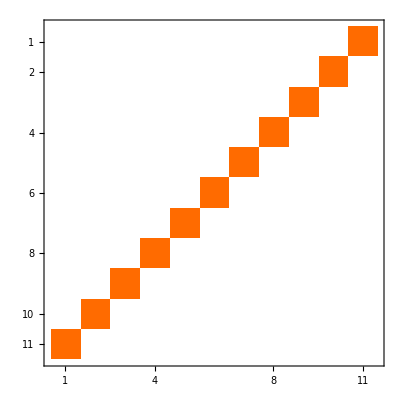

```mathematica
matFull.mat1//MatrixPlot
```

```mathematica
matFull//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 3 | 1 | 3 | 3 | 3 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 0 | 1
0 | 0 | 1 | 1 | 0 | 4 | 2 | 1 | 3 | 2 | 1
0 | 1 | 6 | 3 | 4 | 16 | 4 | 6 | 7 | 4 | 1
1 | 15 | 45 | 15 | 20 | 60 | 10 | 15 | 15 | 6 | 1)

```mathematica
mat1.PartCoeff2[allGraphs6[3,"colofourrealnull"]/.RepNul6]
```

{16,-1,0,0,0,0,0,0,0,0,0}

```mathematica
PartCoeff[allGraphs6[3,"colofour"]/.RepFul6]
```

{1,14,39,12,16,44,6,9,8,2,0}

```mathematica
Det[%443]
```

-1

```mathematica
IntegerPartitions[5]//Length
```

7

```mathematica
IntegerPartitions[6]//Length
```

11

```mathematica
IntegerPartitions[7]//Length
```

15